August 25th 2020,

After the failed matrix multiplication in Fourier Drawing III, I’ve come back again to try. First we’ll define the matrix we’re using. First column is all 1, second column is all cos(kxi) with an xi for the ith row, third column is all sin(kxi) with xi for the ith row and continued. To simplify our job, we can choose xi independently and just let it equal 1,2,3,4.. etc. due to the nature of parameterizing.

```mathematica
Clear[SineMatrix]
SineMatrix[n_]:=Table[Sin[j*i/2*k*2Pi/n]*(1+(-1)^(i))/2,{j,n},{i,n}]
CosineMatrix[n_]:= Table[Cos[j*i/2*k*2Pi/n]*(1+(-1)^(i))/2,{j,1,n},{i,0,n-1}]
TrigMatrix[n_]:=
SineMatrix[n]+CosineMatrix[n]
M=MatrixForm[TrigMatrix[5]]
```

(1 | Sin[(2 k π)/5] | Cos[(2 k π)/5] | Sin[(4 k π)/5] | Cos[(4 k π)/5]
1 | Sin[(4 k π)/5] | Cos[(4 k π)/5] | Sin[(8 k π)/5] | Cos[(8 k π)/5]
1 | Sin[(6 k π)/5] | Cos[(6 k π)/5] | Sin[(12 k π)/5] | Cos[(12 k π)/5]
1 | Sin[(8 k π)/5] | Cos[(8 k π)/5] | Sin[(16 k π)/5] | Cos[(16 k π)/5]
1 | Sin[2 k π] | Cos[2 k π] | Sin[4 k π] | Cos[4 k π])

```mathematica
TestList = {{1,2},{5,7},{2,3},{6,9}}
makePoints[List_]:=List
getX[List_,n_]:=Flatten[List][[2*n-1]]
getY[List_,n_]:=Flatten[List][[2*n]]
FX[Listing_]:=Block[{Points},
Table[getX[Listing,j],{j,1,Dimensions[Listing][[1]]}]
]
FY[Listing_]:=Block[{Points},
Table[getY[Listing,j],{j,1,Dimensions[Listing][[1]]}]
]

HalfRes[Splitthis_]:=
Table[Splitthis[[2*j]],{j,1,Length[Splitthis]/2}]
TestList[[1]]
HalfRes[TestList]
FY[TestList]
```

{{1,2},{5,7},{2,3},{6,9}}

{1,2}

{{5,7},{6,9}}

{2,7,3,9}

Now we’ve defined FX and FY for each of the x(t) and y(t), multiplying the inverse by this will give a vector of the coefficients. This will give the points (1,Y1);(2,Y2);(3,Y3)... etc.

```mathematica
CoefficientAX[XYPoints_]:=Block[{Fvals},
Fvals=FX[XYPoints];
N[Inverse[TrigMatrix[Length[Fvals]]/.k->1]].Fvals
]
CoefficientAY[XYPoints_]:=Block[{Fvals},
Fvals=FY[XYPoints];
N[Inverse[TrigMatrix[Length[Fvals]]/.k->1]].Fvals
]
AX1=CoefficientAX[TestList]
```

Inverse::sing: Matrix {{1,1,0,0},{1,0,-1,0},{1,-1,0,0},{1,0,1,0}} is singular.

Inverse::sing: Matrix {{1.,1.,0.,0.},{1.,0.,-1.,0.},{1.,-1.,0.,0.},{1.,0.,1.,0.}} is singular.

Inverse[{{1.,1.,0.,0.},{1.,0.,-1.,0.},{1.,-1.,0.,0.},{1.,0.,1.,0.}}].{1,5,2,6}

Now we have to take these coefficients and the dot product with a trigonometric vector in order to get f(x)

```mathematica
TrigVector[M_]:=
M[[1]]

PlotXvsT[Points_]:=Block[{TrigVect,Number},
Number= Dimensions[Points][[1]];
TrigVect=TrigVector[TrigMatrix[Number]];
Plot[TrigVect.CoefficientAX[Points]/.k->t,{t,1,Number}]
]
PlotYvsT[Points_]:=Block[{TrigVect,Number},
Number= Dimensions[Points][[1]];
TrigVect=TrigVector[TrigMatrix[Number]];
Plot[TrigVect.CoefficientAY[Points]/.k->t,{t,1,Number}]
]
```

Now we look to produce a final parametric plot that crosses through all of the points. We always want to make sure we’re plotting points on a 0 to 2pi range and just making the increment smaller in t otherwise we’re going to get a squiggly nightmare as t gets very large.

```mathematica
PlotFourierPoints[Points_]:=Block[{TrigVect,Number},
Number= Dimensions[Points][[1]];
TrigVect=TrigVector[TrigMatrix[Number]];

ParametricPlot[{TrigVect.CoefficientAX[Points]/.k->t,TrigVect.CoefficientAY[Points]/.k->t},{t,1,Number},PlotRange-> All]
]

CircleP={{1,0},{0,1},{-1,0},{0,-1}} ;
Smile={{-1,1},{-0.5,0},{0,-0.25},{0.5,0},{1,1}};
(*Items must be given in order you want them to be intersected!*)
PlotFourierPoints[Smile]//AbsoluteTiming;
```

While all this works just fine and is coming along nicely, it’s taking about 20 seconds to solve for 5 points on average which is not great at all if I want to do about 40 points (involves inverting 40x40 matrix). So, Mathematica has inbuilt functions for a reason and I will thus use them instead! LinearSolve is now the love of my life.

```mathematica
ListGenerator[Number_]:=
Table[RandomReal[{-1,1},{1,2}],{Number}]

Testing=ListGenerator[20];

FastAX[XYPoints_,G_]:=Block[{FXVals},
FXVals=FX[XYPoints];
LinearSolve[N[TrigMatrix[Length[FXVals]]/.k->G],FXVals]
]
FastAY[XYPoints_,G_]:=Block[{FYVals},
FYVals=FY[XYPoints];
LinearSolve[N[TrigMatrix[Length[FYVals]]/.k->G],FYVals]
]

(*FastAX[Testing]//AbsoluteTiming
CoefficientAX[Testing]//AbsoluteTiming*)
```

LinearSolve is ridiculously fast compared to the matrix inversion method I was using before, it can solve a 20 long list of points in 0.02 seconds when inverting the matrix was > 2 minutes (still not done)

```mathematica
FastFourierPointsAllPlot[Points_,G_]:=Block[{TrigVect,Number},
Number=Length[Points];
TrigVect=TrigVector[TrigMatrix[Number]];
{"Xplot"->Show[Plot[{TrigVect.FastAX[Points,G]/.k->t},{t,1,Number}],ListPlot[Table[Style[{j,getX[Points,j]},Hue[2]],{j,1,Length[Points]}]]],"Yplot"-> Show[Plot[{TrigVect.FastAY[Points,G]/.k->t},{t,1,Number}],ListPlot[Table[Style[{j,getY[Points,j]},Hue[2]],{j,1,Length[Points]}]]],
"Parametric"-> ParametricPlot[{TrigVect.FastAX[Points,G]/.k->t,TrigVect.FastAY[Points,G]/.k->t},{t,1,Number},PlotRange-> Automatic]}
]
FastFourierPointsPlot[Points_,G_]:=Block[{TrigVect,Number},
Number=Length[Points];
TrigVect=TrigVector[TrigMatrix[Number]];
{"Parametric"-> ParametricPlot[{TrigVect.FastAX[Points,G]/.k->t,TrigVect.FastAY[Points,G]/.k->t},{t,1,Number},PlotRange-> Automatic]}
]
```

Then we can go ahead and graph these, there are still some kinks to iron out (for example, even numbers don’t seem to work for the linear equations and also the length scale of the graph is still not fixed for the number of points.

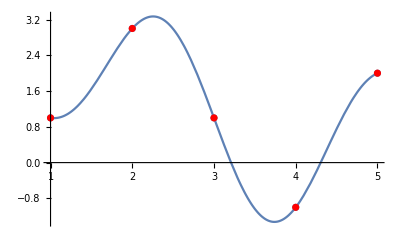
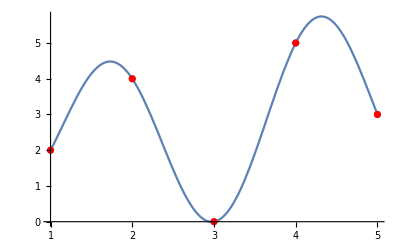
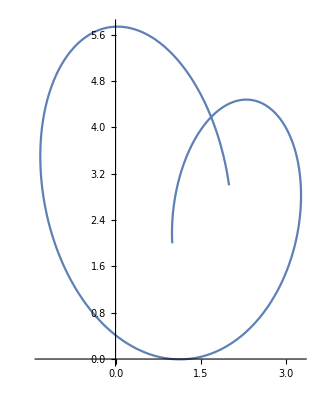
{1.50583,{Xplot→-Graphics-,Yplot→-Graphics-,Parametric→-Graphics-}}

```mathematica
JumpyTest={{1,2},{3,4},{1,0},{-1,5},{2,3}}; 
HeartTest ={{161.171875,158.08984375},{178.5,153.93359375},{180.8046875,156.87890625},{184.11328125,165.29296875},{188.1875,174.078125},{198.6328125,187.71875},{201.19140625,194.69140625},{202.35546875,201.5078125},{202.9453125,209.99609375},{200.09375,214.28515625},{193.12109375,215.28515625},{188.41015625,213.546875},{180.7421875,200.734375},{180.7421875,203.00390625},{177.51953125,208.66015625},{168.578125,215.9765625},{163.578125,216.4296875},{154.4921875,214.91015625},{148.953125,208.515625},{147.38671875,198.79296875},{149.4765625,181.328125},{156.140625,165.2109375},{165.07421875,153.10546875},{171.75,145.32421875},{179.875,137.8828125}};
Length[HeartTest];
FastFourierPointsAllPlot[JumpyTest,1]//AbsoluteTiming (*Whenever it's an even number, it breaks. Will fix later*)
```

Now, we’re going to do a small test on an image since the function is running with good speed. We’ll use this humorous image.

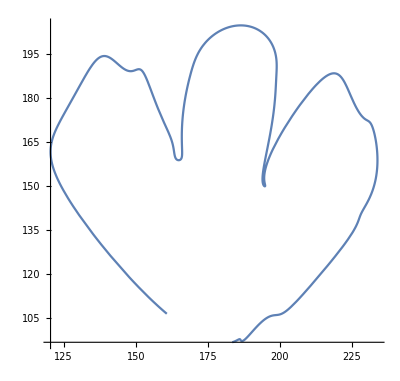
{Parametric→-Graphics-}

```mathematica
Randomshape={{183.48828125,96.68359375},{186.58984375,97.1953125},{191.48046875,101.45703125},{198.6015625,105.95703125},{207.37109375,112.30859375},{222.90234375,130.75},{227.96484375,140.},{232.40234375,149.08203125},{233.2734375,165.66796875},{230.421875,172.30859375},{225.37109375,179.0703125},{218.07421875,188.33984375},{202.76171875,171.5390625},{194.57421875,153.08984375},{194.57421875,149.9765625},{194.890625,158.91015625},{198.2890625,179.3359375},{198.8984375,191.6796875},{192.42578125,203.28515625},{176.2578125,200.8984375},{169.48828125,189.80078125},{166.40234375,174.6640625},{166.08984375,161.16015625},{164.54296875,158.83984375},{163.17578125,162.40625},{160.296875,170.5546875},{154.5390625,184.5703125},{150.08984375,189.58984375},{143.5078125,191.81640625},{134.62890625,190.89453125},{122.83203125,170.33984375},{126.8671875,145.22265625},{160.76953125,106.40625}};
Length[Randomshape];
(*FastFourierPointsPlot[Randomshape,1]*)
```

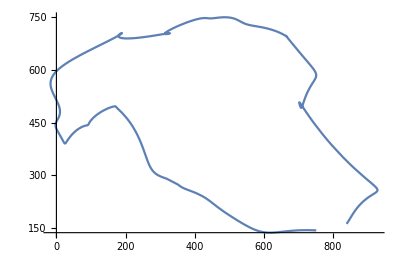
{Parametric→-Graphics-}

```mathematica
Doog={{790.1663544164669,141.28055055955224},{839.9636290967227,162.06993155475607},{888.6186300959233,206.0796862509991},{908.1544389488411,241.10355465627492},{900.756020183853,274.42279926059143},{890.8035946243007,295.2941896482813},{826.6956809552358,364.35195593525174},{732.9530875299761,465.7448541167066},{708.6021557753797,497.4766311950439},{704.9175909272583,498.7594924060751},{707.2665742406076,504.9160546562749},{720.5345223820945,522.5070693445243},{745.8109887090328,558.4857613908873},{751.8738259392487,583.8383792965627},{740.9138564148682,614.3751623701039},{704.3200939248602,649.3873151478817},{684.4152428057555,665.1565497601919},{664.9555855315748,696.8414643285372},{658.0960856314949,701.8030325739409},{655.0265912270185,701.8030325739409},{612.4930055955236,714.5203462230215},{579.6130970223821,724.0920138888889},{564.3007718824941,729.8326713629097},{526.4944419464429,741.1733987809753},{496.7426059152678,747.4588329336531},{468.36735611510795,748.8647082334132},{464.9229616306955,748.8647082334132},{430.00453387290173,747.7927283173461},{376.0716426858513,740.5641861510792},{348.25874300559553,723.4652278177458},{323.2634517386091,716.5412919664269},{321.30694194644286,702.5294014788169},{285.820306254996,698.2004771183053},{282.3700539568345,697.7259942046363},{243.46245503597123,694.2405950239809},{179.84073990807354,695.447304656275},{176.27333133493204,694.849807653877},{171.83310851318947,693.5786620703437},{72.26199040767388,671.4595573541167},{10.778377298161473,605.9809152677858},{0.26360161870503873,563.2305905275779},{0.26360161870503873,513.8960831334932},{0.8610986211031246,460.91215777378096},{0.8610986211031246,454.5681454836131},{6.373301358912869,426.91340677458027},{11.657049360511593,411.7943894884092},{17.913194444444443,396.3590502597921},{30.36690647482014,397.0092675859312},{49.24078237410073,407.2018635091926},{76.01684902078337,438.8399155675459},{86.93581384892086,446.70695943245397},{95.11332184252599,449.7237335131894},{125.91956434852118,467.8829561350919},{144.84030275779378,488.82464028776974},{155.43123001598724,498.5427532973621},{173.0515337729816,494.56529776179053},{201.00502098321346,469.3415517585931},{212.56834532374103,451.1764713229416},{222.7609412470024,428.5477368105515},{264.076101618705,340.6219524380495},{286.2655000999201,318.08108513189444},{313.0357089328537,292.716751598721},{330.3924110711431,280.22203487210226},{355.4169914068745,271.195143884892},{375.39799410471625,262.2092575939248},{402.02175759392486,250.58735511590714},{424.42203737010396,237.99891336930443},{458.69610561550763,215.83880395683445},{523.3370803357315,172.23909622302153},{533.6351169064749,166.19383243405264},{567.7920288768986,153.48823441246986},{625.2806130095925,137.1976543764987},{663.0225069944046,136.6001573741006},{752.1608588129498,143.41865257793756},{756.5952238209434,143.41865257793756},{794.8174585331735,143.41865257793756}};
Length[HalfRes[Doog]];
Dograph=HalfRes[Doog][[1;;37]];
(*FastFourierPointsPlot[Dograph,1]*)
```

Originally, I was incrementing t by one and keeping the period constant. This was creating a considerable amount of chaos for really large sets since their t value would go up to their length and the longest wavelength wave i was using was still 2pi periodic meaning that we got sharp up and down vibrations which led to chaotic and indecipherable images. Now, I’ve fixed it to increment by a scaled amount depending on the number and the images have come out much more clearly.

August 27th. 
Now we’ll do a test on a face by sampling  points manually and then try and implement some sort of edge detection in order to get the points automatically. (Unfortunately this does not work since the points are sampled in a specific order which is not the same order that one would trace them out with.

```mathematica
Shaq=-Graphics-;
ShaqEdge=EdgeDetect[Shaq]
ShaqP=PixelValuePositions[ImageResize[ShaqEdge,100], 1];
```

-Graphics-

This has worked beautifully! The only problem is it’s ridiculously large as a set, we need to work on making a function to eliminate points with a certain frequency to adjust the effective “resolution” to greatly speed up processing times. (on average there are about 1400 coordinates or so, we want to reduce this, if we can to maybe 50 at most)

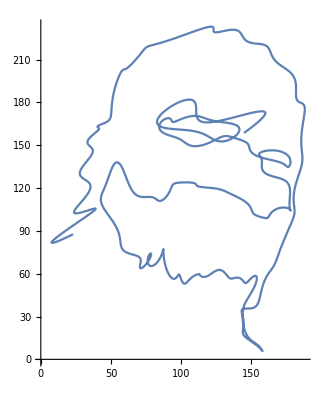
{Parametric→-Graphics-}

```mathematica
ResReduce[Points_,Resolution_]:=
Table[Points[[Resolution*j]],{j,1,If[IntegerQ[Length[Points]/Resolution]==True,Length[Resolution]/Points,Floor[Length[Points]/Resolution]]}]
ShaqHandpicked={{150.23828125,158.5115966796875},{144.96160888671875,158.56964111328125},{141.0833740234375,164.98822021484375},{134.1180419921875,168.56646728515625},{125.47119140625,171.27618408203125},{110.81707763671875,176.1148681640625},{99.177490234375,177.818115234375},{90.22100830078125,175.33343505859375},{88.70166015625,171.0003662109375},{93.78955078125,161.361572265625},{108.40740966796875,156.72607421875},{120.891357421875,155.33734130859375},{130.45025634765625,153.0413818359375},{138.4970703125,156.15753173828125},{139.2108154296875,160.90191650390625},{134.1131591796875,165.46966552734375},{126.53570556640625,168.29547119140625},{115.48406982421875,169.456787109375},{108.342041015625,168.919677734375},{99.82586669921875,168.15277099609375},{97.353271484375,167.61566162109375},{93.15814208984375,167.61566162109375},{91.0411376953125,167.61566162109375},{85.5927734375,165.89306640625},{85.30242919921875,163.44952392578125},{91.23956298828125,157.02606201171875},{97.48150634765625,154.3575439453125},{103.55169677734375,151.3260498046875},{108.59613037109375,150.4139404296875},{118.90020751953125,151.205078125},{128.449462890625,155.3978271484375},{132.45831298828125,156.44061279296875},{143.35272216796875,156.06317138671875},{144.71246337890625,152.85748291015625},{144.71246337890625,150.5615234375},{149.48101806640625,146.29620361328125},{156.6011962890625,144.17681884765625},{164.1085205078125,139.70098876953125},{166.9246826171875,138.56146240234375},{175.5787353515625,135.08001708984375},{178.67071533203125,137.5767822265625},{178.00054931640625,139.7178955078125},{165.2335205078125,148.97442626953125},{163.5447998046875,146.37115478515625},{159.054443359375,145.16876220703125},{156.2431640625,142.4542236328125},{155.14959716796875,139.865478515625},{157.6754150390625,134.92755126953125},{163.2230224609375,131.71466064453125},{168.2069091796875,127.45416259765625},{174.73681640625,120.30975341796875},{177.8311767578125,116.8282470703125},{180.0013427734375,108.42578125},{178.17230224609375,104.2620849609375},{175.04644775390625,103.577392578125},{172.0150146484375,106.29193115234375},{162.77545166015625,103.11285400390625},{162.77545166015625,100.33062744140625},{161.35528564453125,97.74188232421875},{157.01007080078125,99.65802001953125},{154.7794189453125,101.5693359375},{150.6544189453125,104.02984619140625},{146.96002197265625,108.78387451171875},{143.37213134765625,112.0185546875},{139.8228759765625,114.66778564453125},{131.7301025390625,117.6605224609375},{127.45751953125,118.87261962890625},{119.51953125,120.24444580078125},{115.8638916015625,120.59765625},{111.11224365234375,122.02752685546875},{108.99530029296875,122.73394775390625},{104.98638916015625,123.9364013671875},{102.04931640625,125.53076171875},{94.571044921875,122.634765625},{91.22021484375,117.27099609375},{90.12664794921875,114.68231201171875},{87.17498779296875,111.0411376953125},{83.16851806640625,111.566162109375},{80.8580322265625,111.74273681640625},{75.30316162109375,113.6976318359375},{68.89666748046875,116.90087890625},{63.67572021484375,120.88555908203125},{57.06842041015625,130.80255126953125},{55.24176025390625,137.7364501953125},{52.96514892578125,136.32598876953125},{48.01513671875,126.68475341796875},{44.1126708984375,118.642822265625},{42.8134765625,112.369384765625},{45.71185302734375,106.3282470703125},{50.7901611328125,97.4830322265625},{52.5006103515625,92.1337890625},{56.90631103515625,81.39422607421875},{60.09747314453125,77.49658203125},{64.88055419921875,73.5965576171875},{67.55633544921875,68.72882080078125},{71.20477294921875,67.87237548828125},{72.18701171875,70.79498291015625},{73.718505859375,65.196533203125},{75.3394775390625,63.14251708984375},{78.3564453125,74.17724609375},{77.75885009765625,69.97235107421875},{77.75885009765625,65.59332275390625},{80.952392578125,62.6102294921875},{86.85809326171875,75.06756591796875},{88.00726318359375,72.62158203125},{88.23712158203125,68.52801513671875},{91.621826171875,53.138427734375},{95.68634033203125,56.515869140625},{97.85894775390625,62.5400390625},{99.02508544921875,58.872314453125},{99.4339599609375,55.07391357421875},{102.48236083984375,53.0150146484375},{107.44207763671875,61.712646484375},{108.2525634765625,57.76422119140625},{108.61785888671875,54.6505126953125},{112.9654541015625,59.71905517578125},{113.5703125,62.7142333984375},{114.41229248046875,58.2117919921875},{119.66229248046875,62.356201171875},{121.0389404296875,59.57635498046875},{123.62762451171875,59.7529296875},{129.38818359375,62.0997314453125},{131.97686767578125,60.99407958984375},{135.146240234375,56.6876220703125},{135.978515625,59.6053466796875},{141.46319580078125,57.08441162109375},{143.89227294921875,53.43115234375},{146.1737060546875,53.455322265625},{149.38421630859375,57.72796630859375},{152.13018798828125,58.2408447265625},{152.2899169921875,54.6263427734375},{152.46893310546875,51.0020751953125},{151.5882568359375,48.45452880859375},{145.2640380859375,38.13348388671875},{144.13421630859375,25.8406982421875},{144.57696533203125,23.78179931640625},{148.07293701171875,16.310791015625},{150.9229736328125,12.7034912109375},{154.18426513671875,10.00592041015625},{156.9495849609375,7.59381103515625},{158.6383056640625,4.7703857421875},{157.29315185546875,6.91156005859375},{152.6915283203125,11.1260986328125},{147.51165771484375,14.404296875},{145.3970947265625,18.4954833984375},{144.42938232421875,21.751953125},{143.31884765625,29.68743896484375},{143.4979248046875,32.445556640625},{146.04791259765625,34.90118408203125},{148.33905029296875,35.58587646484375},{153.054443359375,38.1431884765625},{156.163330078125,42.81011962890625},{160.343994140625,54.75213623046875},{161.94317626953125,59.34405517578125},{165.6641845703125,66.9820556640625},{168.80694580078125,71.42156982421875},{174.27471923828125,84.03857421875},{177.94970703125,93.689453125},{179.0335693359375,98.8184814453125},{180.62310791015625,108.5250244140625},{181.59326171875,118.31134033203125},{183.77313232421875,128.4896240234375},{185.36505126953125,138.45257568359375},{186.2698974609375,145.83892822265625},{187.8134765625,160.04058837890625},{187.60296630859375,168.7987060546875},{186.6231689453125,174.6414794921875},{185.321533203125,179.7633056640625},{184.17718505859375,184.43023681640625},{182.1182861328125,189.32464599609375},{178.22552490234375,197.548095703125},{174.4827880859375,203.68603515625},{169.8714599609375,209.68603515625},{163.94158935546875,214.99896240234375},{159.17059326171875,218.80224609375},{154.36810302734375,221.08367919921875},{148.03424072265625,224.4417724609375},{143.58013916015625,226.95794677734375},{137.5220947265625,229.2127685546875},{131.771240234375,230.21197509765625},{127.000244140625,230.96923828125},{123.25506591796875,230.96923828125},{115.35821533203125,230.96923828125},{110.543701171875,230.1007080078125},{90.90325927734375,224.8167724609375},{80.26043701171875,220.27081298828125},{78.2039794921875,219.1240234375},{70.65313720703125,213.35626220703125},{66.95880126953125,210.034423828125},{60.2764892578125,203.28924560546875},{57.0321044921875,199.8126220703125},{55.42803955078125,197.4537353515625},{52.87078857421875,190.258544921875},{50.4127197265625,174.70196533203125},{47.96673583984375,166.45196533203125},{45.10943603515625,165.3970947265625},{42.76507568359375,164.66644287109375},{40.856201171875,162.385009765625},{39.0731201171875,159.861572265625},{37.534423828125,157.5970458984375},{36.0731201171875,154.072021484375},{34.911834716796875,149.409912109375},{34.527130126953125,145.655029296875},{32.894073486328125,138.82757568359375},{31.34808349609375,131.3057861328125},{30.9271240234375,126.22991943359375},{30.494049072265625,119.16778564453125},{30.494049072265625,112.100830078125},{30.494049072265625,107.2886962890625},{29.91339111328125,103.17822265625},{29.5601806640625,100.07171630859375},{28.502899169921875,97.42254638671875},{25.839202880859375,92.4119873046875},{22.98675537109375,87.6192626953125},{20.228668212890625,83.4893798828125},{17.347198486328125,79.54339599609375}};
Length[ShaqHandpicked];
ShaqPLD=HalfRes[ShaqHandpicked][[1;;107]];
FastFourierPointsPlot[ShaqPLD,1] (*This generates spooky Shaq, pretty decent image*)
```

Now for the final, we’re going to manually put my DOS in and see how long it takes, we’ll try somewhere around 99 points for decent rendering.

```mathematica
Pietro= -Graphics-;
EdgeDetect[Pietro]
```

-Graphics-

```mathematica
PietroPoints={{94.30859375,269.4453125},{95.23046875,266.21875},{97.07421875,261.37890625},{99.609375,255.6171875},{102.14453125,250.31640625},{105.140625,247.08984375},{107.4453125,245.4765625},{109.51953125,248.421875},{109.0703125,253.18359375},{107.9375,257.91015625},{107.48828125,268.7578125},{107.83984375,281.46484375},{107.26171875,294.4296875},{107.26171875,296.69921875},{107.0390625,304.875},{107.0390625,312.3828125},{108.65234375,321.0234375},{109.34375,326.91796875},{109.578125,333.9453125},{110.0390625,338.94140625},{112.40625,347.76953125},{113.09765625,350.95703125},{119.296875,365.30859375},{123.00390625,374.4921875},{127.3828125,383.59375},{128.53515625,386.3203125},{131.94921875,392.59765625},{138.6328125,398.48828125},{145.546875,400.98046875},{148.7734375,400.2890625},{155.6875,392.9140625},{158.68359375,387.15234375},{165.96484375,385.3046875},{173.109375,385.06640625},{172.66796875,387.78515625},{165.15625,392.54296875},{165.6171875,396.39453125},{168.61328125,397.98046875},{172.30078125,399.11328125},{183.77734375,398.421875},{187.6484375,398.12890625},{194.46875,399.94140625},{193.3359375,403.56640625},{187.890625,405.60546875},{176.62109375,404.390625},{159.921875,404.90625},{157.43359375,409.4375},{161.12109375,413.5234375},{168.7265625,417.15234375},{172.828125,418.34765625},{179.51171875,419.70703125},{187.34765625,421.06640625},{189.8828125,421.51953125},{197.94921875,422.42578125},{200.71484375,422.65234375},{210.53125,421.9609375},{222.28125,419.97265625},{226.3359375,418.6953125},{240.453125,415.44921875},{251.640625,409.04296875},{259.7265625,398.07421875},{261.80078125,395.078125},{267.33203125,387.93359375},{272.484375,375.50390625},{279.6328125,348.8046875},{278.94921875,340.27734375},{278.49609375,335.71484375},{278.04296875,322.58203125},{278.50390625,317.65234375},{281.73046875,310.73828125},{284.49609375,309.35546875},{295.46484375,307.7421875},{304.7734375,306.6328125},{309.3359375,302.9453125},{307.75,299.94921875},{303.66796875,294.6484375},{301.85546875,292.11328125},{299.0703125,284.5546875},{297.12890625,280.453125},{293.765625,271.55859375},{292.9609375,267.2734375},{289.8359375,257.578125},{287.796875,252.046875},{281.2421875,250.13671875},{279.4296875,252.62890625},{279.4296875,259.6796875},{280.12109375,268.68359375},{280.5859375,280.83203125},{282.19921875,290.08984375},{283.8125,296.44140625},{285.88671875,301.65234375},{285.8984375,306.41796875},{282.7265625,308.23046875},{274.11328125,307.76953125},{260.7109375,311.36328125},{255.52734375,312.1015625},{252.5703125,312.328125},{245.06640625,313.0078125},{240.4765625,314.09765625},{228.5390625,317.171875},{217.484375,318.42578125},{213.65625,318.1953125},{202.57421875,315.59765625},{200.30859375,313.75390625},{198.10546875,305.734375},{198.10546875,302.27734375},{200.640625,291.03125},{206.546875,281.76953125},{208.62109375,280.38671875},{212.5390625,278.7734375},{215.07421875,278.08203125},{224.76953125,277.16015625},{228.59375,276.46875},{240.296875,276.68359375},{250.01953125,280.5625},{257.0703125,285.73828125},{257.76171875,288.23046875},{258.453125,293.44921875},{260.06640625,298.453125},{266.75,299.8125},{281.17578125,299.8125},{294.421875,300.71875},{295.34375,305.26171875},{294.890625,307.3046875},{291.4921875,307.3046875},{277.7578125,307.36328125},{273.23828125,307.36328125},{262.46484375,307.97265625},{260.87890625,310.6953125},{259.97265625,313.64453125},{257.9296875,316.14453125},{255.2109375,316.14453125},{252.7109375,315.9140625},{233.1015625,315.6796875},{221.81640625,315.09375},{213.62109375,315.09375},{203.390625,314.5078125},{199.5390625,311.28125},{198.41796875,305.98046875},{196.15625,305.0546875},{188.26953125,305.28125},{182.8203125,304.8203125},{176.67578125,306.40625},{173.73046875,310.484375},{171.46484375,315.6953125},{167.15625,316.375},{151.140625,316.72265625},{146.6171875,317.40234375},{130.859375,318.43359375},{122.67578125,314.7890625},{123.3671875,309.94921875},{123.84765625,307.875},{97.1953125,306.74609375},{99.5078125,305.36328125},{104.578125,303.2890625},{111.4921875,302.36328125},{117.0234375,303.5},{117.71484375,300.04296875},{117.9453125,293.63671875},{118.63671875,287.18359375},{121.40234375,282.8046875},{126.47265625,279.578125},{130.8046875,278.59375},{143.96875,277.359375},{161.18359375,277.52734375},{167.95703125,278.20703125},{173.71875,279.79296875},{177.23828125,287.03515625},{180.0234375,296.90625},{181.23828125,301.421875},{186.26171875,301.12890625},{190.82421875,301.12890625},{197.18359375,301.125},{197.64453125,294.53515625},{198.92578125,286.1484375},{202.21484375,277.66796875},{204.75,270.75390625},{206.328125,262.13671875},{207.25,259.37109375},{208.6953125,253.65625},{207.5625,249.73828125},{205.0625,246.97265625},{198.69140625,243.9765625},{192.59765625,242.59375},{187.015625,242.296875},{177.09375,243.71875},{171.41015625,248.0234375},{167.63671875,252.31640625},{165.30859375,264.82421875},{164.62890625,267.4765625},{162.171875,265.046875},{157.39453125,258.36328125},{154.20703125,255.13671875},{147.8359375,248.453125},{145.55859375,245.91796875},{140.98828125,237.484375},{138.03125,234.48828125},{133.25,227.34375},{134.234375,223.05859375},{136.76953125,219.6015625},{138.61328125,217.52734375},{143.2421875,209.6015625},{147.390625,205.68359375},{153.10546875,204.00390625},{164.2265625,204.86328125},{175.0546875,205.0859375},{187.76953125,205.14453125},{196.6171875,205.43359375},{204.22265625,207.0234375},{212.01171875,208.4453125},{215.0078125,208.66796875},{223.90234375,210.31640625},{231.,212.19140625},{236.9453125,214.81640625},{240.6328125,215.94921875},{247.26953125,219.18359375},{248.19921875,221.2265625},{238.44921875,222.6015625},{227.1796875,222.828125},{216.765625,222.4140625},{201.64453125,223.16796875},{190.62109375,222.4140625},{184.47265625,221.72265625},{176.4453125,223.0390625},{170.0703125,223.94140625},{159.6171875,226.16796875},{149.97265625,227.42578125},{141.20703125,227.1953125},{137.125,227.421875},{129.76953125,226.9609375},{129.546875,223.50390625},{132.54296875,220.73828125},{137.58984375,217.421875},{145.1015625,211.640625},{159.1484375,201.2890625},{164.5390625,198.2734375},{174.09765625,185.23828125},{175.25390625,182.2421875},{183.04296875,176.6484375},{191.109375,173.390625},{205.54296875,173.26953125},{207.80078125,174.69140625},{207.57421875,179.9921875},{194.8671875,180.56640625},{192.37109375,181.26171875},{188.765625,182.00390625},{171.2265625,184.47265625},{161.515625,185.2109375},{156.96484375,181.984375},{157.65625,179.44921875},{164.77734375,172.90625},{173.578125,168.61328125},{177.6796875,166.875},{183.671875,162.95703125},{188.51171875,161.5703125},{195.609375,159.203125},{202.24609375,155.16015625},{205.703125,154.9296875},{211.00390625,154.9296875},{214.69140625,155.15234375},{216.765625,156.28515625},{231.74609375,158.55859375},{246.73828125,160.46484375},{256.4296875,162.70703125},{264.76953125,165.3203125},{269.37890625,166.453125},{271.453125,166.90625},{274.44921875,168.4921875},{278.13671875,170.3046875},{281.59375,172.5703125},{283.4375,175.98046875},{285.63671875,182.046875},{285.63671875,184.7734375},{285.41015625,191.57421875},{284.95703125,194.30078125},{284.50390625,201.0546875},{284.50390625,206.40625},{285.1953125,210.71484375},{285.48828125,218.59765625},{285.94921875,222.6875},{285.94921875,224.73046875},{287.10546875,228.5859375},{291.0234375,229.7109375},{293.09765625,231.0703125},{295.171875,232.65625},{298.859375,237.1953125},{301.1640625,240.3671875},{304.62109375,244.68359375},{306.234375,247.64453125},{309.921875,254.2578125},{310.84375,258.12109375},{315.50390625,270.31640625},{318.45703125,280.15625},{319.734375,285.27734375},{319.96484375,292.30859375},{319.,296.1328125},{318.09375,299.30859375},{316.734375,302.03515625},{312.8828125,306.34375},{309.9375,308.8359375},{307.671875,312.92578125},{306.0859375,317.703125},{304.6015625,326.0234375},{303.6953125,334.296875},{302.5,341.9296875},{302.50390625,349.14453125},{304.421875,357.94140625},{304.890625,364.46484375},{303.46875,370.80859375},{301.8828125,374.2109375},{299.6171875,378.3046875},{298.7109375,380.34375},{296.21484375,383.9765625},{294.625,386.24609375},{291.6796875,390.109375},{289.41015625,392.609375},{285.08984375,398.07421875},{280.64453125,403.49609375},{278.375,405.9921875},{275.4296875,409.1640625},{273.16015625,411.890625},{269.30078125,415.75},{265.44140625,419.15234375},{256.796875,424.59375},{250.86328125,427.54296875},{248.1328125,428.67578125},{244.046875,430.26171875},{240.90234375,432.140625},{230.79296875,434.78515625},{226.26953125,436.2109375},{220.3828125,436.953125},{216.3203125,436.953125},{208.68359375,436.953125},{204.390625,436.953125},{199.65234375,436.72265625},{195.7734375,436.4921875},{188.73828125,435.5703125},{186.46875,435.109375},{181.,432.8046875},{176.2890625,432.05078125},{168.1015625,430.41796875},{163.17578125,428.91015625},{160.453125,427.296875},{155.48828125,423.484375},{151.47265625,420.9921875},{144.296875,415.77734375},{142.0234375,413.2421875},{133.625,407.62109375},{123.578125,403.203125},{118.0703125,398.16015625},{110.734375,392.95703125},{103.48828125,390.80859375},{101.046875,384.6171875},{103.24609375,378.02734375},{102.9609375,367.51953125},{101.46875,364.109375},{95.72265625,358.0234375},{92.765625,354.796875},{89.58984375,350.6484375},{88.33203125,346.36328125},{88.79296875,337.0859375},{89.90625,322.3046875},{90.78125,312.2109375},{93.2734375,306.25},{95.01953125,301.2265625},{93.20703125,297.76953125},{92.23828125,291.87109375},{92.01171875,288.4140625},{92.2421875,283.11328125},{93.51953125,278.3671875},{93.5234375,265.5703125},{92.0234375,248.875},{95.421875,241.53125},{99.0625,238.41015625},{103.2109375,236.3359375},{106.20703125,235.18359375},{109.6171875,234.4296875},{111.,232.35546875},{111.29296875,226.91796875},{112.5703125,218.94921875},{114.265625,211.48828125},{115.953125,202.671875},{116.64453125,196.7734375},{117.93359375,189.33984375},{119.90234375,183.90234375},{122.8984375,179.75390625},{126.5859375,176.98828125},{130.50390625,173.9921875},{133.5,172.83984375},{137.1875,171.45703125},{139.72265625,170.53515625},{142.94921875,168.69140625},{146.8671875,165.6953125},{148.94140625,163.8515625},{151.30859375,160.44140625},{154.02734375,158.2421875},{158.17578125,153.86328125},{160.48046875,152.7109375},{165.87109375,150.32421875},{168.63671875,148.94140625},{172.78515625,147.7890625},{177.80859375,147.7890625},{182.78515625,148.015625},{187.76171875,148.015625},{193.10546875,149.046875},{198.8203125,148.81640625},{204.50390625,148.81640625},{211.046875,148.81640625},{213.8125,148.81640625},{216.1171875,148.5859375}};
```

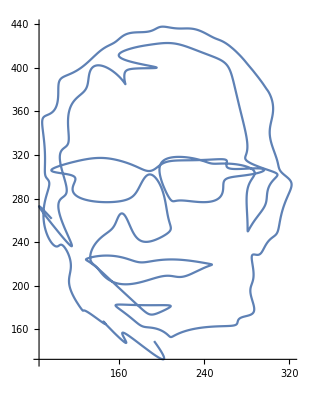
{Parametric→-Graphics-}

```mathematica
PietroFull=ResReduce[PietroPoints,3][[1;;135]];
ReducedPietro =HalfRes[HalfRes[PietroPoints]][[1;;99]];
FastFourierPointsPlot[PietroFull,1]
```

Now we’ll do a hammer and sickle

73

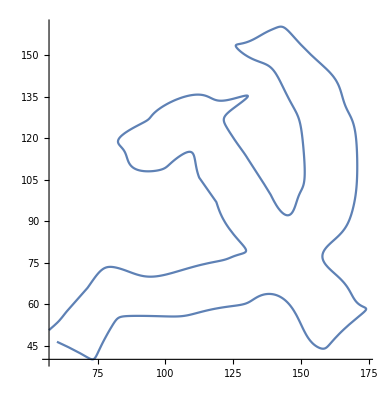
{Parametric→-Graphics-}

```mathematica
Hammersickle={{56.6015625,48.05859375},{60.05859375,46.4453125},{65.12890625,44.6015625},{71.3046875,40.78515625},{73.37890625,39.40234375},{75.578125,43.453125},{78.11328125,48.},{80.87890625,53.0078125},{83.18359375,55.73828125},{86.1796875,55.73828125},{94.3046875,55.328125},{99.89453125,55.6171875},{106.9921875,56.296875},{110.6328125,56.5859375},{121.04296875,58.7109375},{123.76171875,59.2265625},{129.24609375,60.87890625},{132.1953125,61.62109375},{138.32421875,63.94921875},{141.55078125,63.01171875},{146.16015625,57.94140625},{150.140625,52.2265625},{151.5234375,49.921875},{156.15234375,44.484375},{158.2265625,43.5625},{160.53125,45.6015625},{164.91015625,49.234375},{169.51953125,54.2421875},{171.82421875,56.515625},{173.4375,58.7890625},{171.625,60.828125},{168.8984375,62.87109375},{166.95703125,66.01953125},{162.8671875,70.5703125},{158.76953125,74.20703125},{157.875,78.0703125},{161.74609375,81.83203125},{164.05078125,85.0078125},{166.125,88.6484375},{168.66015625,93.203125},{168.484375,97.42578125},{170.453125,103.9609375},{171.60546875,111.48828125},{170.28515625,118.66796875},{169.37890625,123.1796875},{167.765625,128.52734375},{166.6328125,131.265625},{164.81640625,136.00390625},{163.5546875,138.92578125},{159.4375,144.76953125},{156.9765625,147.171875},{149.02734375,154.6015625},{145.87890625,156.7734375},{142.92578125,160.171875},{140.88671875,159.94140625},{138.83984375,159.01953125},{135.89453125,157.17578125},{133.16015625,156.0234375},{128.8828125,154.80859375},{126.8359375,153.88671875},{124.609375,152.44140625},{127.60546875,151.2890625},{130.140625,150.13671875},{135.30078125,147.2890625},{138.94140625,144.3984375},{141.48046875,141.86328125},{145.1875,136.65625},{146.875,131.5546875},{149.3671875,125.2421875},{150.05859375,122.70703125},{151.04296875,117.22265625},{151.2734375,108.22265625},{150.984375,105.04296875},{149.7890625,100.7109375},{149.109375,98.40625},{147.296875,94.2578125},{143.6640625,91.23828125},{142.75390625,93.28125},{141.16796875,96.234375},{138.44921875,100.08984375},{136.40625,102.81640625},{134.8203125,105.3203125},{132.1953125,109.37890625},{130.8359375,111.65234375},{128.796875,115.296875},{126.7578125,117.56640625},{124.8828125,120.25390625},{122.390625,124.125},{120.83984375,127.23046875},{122.9140625,129.04296875},{125.91015625,131.08203125},{130.015625,134.609375},{127.73828125,134.37890625},{124.79296875,134.14453125},{119.62890625,134.37109375},{116.43359375,134.59765625},{108.58203125,134.59765625},{105.2890625,134.3671875},{101.2265625,131.70703125},{95.0546875,128.2109375},{92.8203125,126.53515625},{90.09765625,124.69140625},{84.859375,120.54296875},{82.5859375,119.16015625},{83.97265625,117.0859375},{85.125,114.78125},{86.73828125,112.24609375},{88.58203125,109.01953125},{92.74609375,106.359375},{97.5859375,108.3984375},{100.12109375,109.76171875},{102.1953125,111.12109375},{105.375,112.7734375},{108.83203125,115.03515625},{109.29296875,112.73046875},{111.59765625,108.3515625},{112.98046875,106.27734375},{116.45703125,100.1484375},{117.83984375,98.07421875},{119.64453125,94.25},{122.19921875,88.62890625},{126.54296875,83.53515625},{131.15234375,79.38671875},{129.14453125,78.6328125},{127.09765625,77.703125},{124.37109375,77.01171875},{120.94921875,75.3984375},{118.67578125,75.3984375},{113.55078125,74.05859375},{106.80078125,72.5390625},{101.5,70.76953125},{94.68359375,69.94921875},{91.05078125,70.17578125},{86.3203125,71.82421875},{83.8203125,72.50390625},{80.21484375,73.47265625},{77.72265625,73.9140625},{75.90625,71.83984375},{73.40625,68.84375},{71.296875,65.89453125},{67.57421875,61.90625},{65.984375,59.83203125},{64.16796875,57.52734375},{61.89453125,55.22265625},{60.078125,53.1484375},{57.1328125,50.61328125},{55.08984375,49.45703125}};
Length[HalfRes[Hammersickle]]
FastFourierPointsPlot[HalfRes[Hammersickle],1]
```

29th August 2020.

Earlier in the sheet we encountered a problem. We could use edge-detection in order to draw a list of pixels for an image automatically which is fantastic, but then the ordering was wrong. We shall now attempt to create a reordering function to sort the output out.

```mathematica
Dist[P1_,P2_]:=
(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2
Sort[{{1,2},{6,100},{3,4},{50,50},{20,30}},Dist[#1,#2]>Dist[#2,#1]&]
```

{{20,30},{50,50},{3,4},{6,100},{1,2}}